```mathematica
Quit[];
```

```mathematica
StringJoin[NotebookDirectory[], "AdaptiveDynamicsTools.m"]//Get;
```

# Supplement - Detailed analysis

## Ecological dynamics

Consider a population that is monomorphic with respect to the ecological trait x. The transition matrix of the population dynamics is the product of a migration matrix and a local growth matrix,

```mathematica
Λ =M.Q;
M={{1-m,m},{m,1-m}};
Q={{Subscript[r, 1],0},{0,Subscript[r, 2]}};
MatrixForm[M].MatrixForm[Q]
```

(1-m | m
m | 1-m).(r_1 | 0
0 | r_2)

where r_j=r_j(y,x) is the within-patch geometric growth rate of the mutant.

```mathematica
Subscript[r, 1][y_,x_]:=1-d+1/2 Subscript[W, 1][y,x](1+A[y,x])
Subscript[r, 2][y_,x_]:=1-d+1/2 Subscript[W, 2][y,x](1+A[y,x])
```

where the attractiveness is given by

```mathematica
A[y_,x_]:=Exp[-α(y-x)^2]
```

and the reproductive success W_j in patch j is given by

```mathematica
Subscript[W, 1][y_,x_]:=Subscript[e, 1][y]Subscript[R, 11][x]+Subscript[e, 2][y]Subscript[R, 21][x]
Subscript[W, 2][y_,x_]:=Subscript[e, 1][y]Subscript[R, 12][x]+Subscript[e, 2][y]Subscript[R, 22][x]
```

where e_i is the attack rate of the organisms on resource i. The resources follow dynamics of the following form:

```mathematica
R'[t]==a-(b+N e) R[t];
```

Where a is the resource inflow rate, b is the resource outflow rate, N is the consumer population size and e is the attack rate of the consumer. Assuming that the dynamics of the resources are fast relative to the consumer population dynamics, the equilibrium resource concentrations have the form

```mathematica
resources=Solve[a-(b + N e) R == 0,R]
```

{{R→a/(b+e N)}}

The equilibrium resource concentration R_ij of resource i in patch j are therefore given by

```mathematica
Subscript[R, 11][x_]:=R/.resources/.e->Subscript[e, 1][x]/.N->Subscript[N, 1]//First
Subscript[R, 12][x_]:=h R/.resources/.e->Subscript[e, 1][x]/.N->Subscript[N, 2]//First
Subscript[R, 21][x_]:=h R/.resources/.e->Subscript[e, 2][x]/.N->Subscript[N, 1]//First
Subscript[R, 22][x_]:=R/.resources/.e->Subscript[e, 2][x]/.N->Subscript[N, 2]//First
```

where the attack rates are given by

```mathematica
Subscript[e, 1][x_]:=Exp[-s(x+1)^2]
Subscript[e, 2][x_]:=Exp[-s(x-1)^2]
```

where s is the ecological selection coefficient.

## Invasion analysis

The invasion fitness of a mutant is the leading eigenvalue of the transition matrix. Here we assume that the mutant is initially at low density, sufficiently so that it does not affect the resource dynamics and therefore the density-dependence component of the population dynamics. The invasion fitness is

```mathematica
λ = Λ//Eigenvalues//Last
lambda[y_,x_]:=λ/.Subscript[r, 1]->Subscript[r, 1][y,x]/.Subscript[r, 2]->Subscript[r, 2][y,x]
```

1/2 (r_1-m r_1+r_2-m r_2+√((-r_1+m r_1-r_2+m r_2)^2-4 (r_1 r_2-2 m r_1 r_2)))

We assume that mutations are rare, so the mutant arises in a resident population at ecological equilibrium. This demographic equilibrium condition is given by

```mathematica
dmg={Subscript[N, 1],Subscript[N, 2]}==Λ.{Subscript[N, 1],Subscript[N, 2]}/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x];
```

Here we use a numerical search algorithm to find this equilibrium given some parameter values. For this model we used the following starting conditions for the root search algorithm:

```mathematica
init={{Subscript[N, 1],1000},{Subscript[N, 2],1000}};
```

We can have a look at the pairwise invasibility plot to predict the adaptive dynamics under certain parameter values:

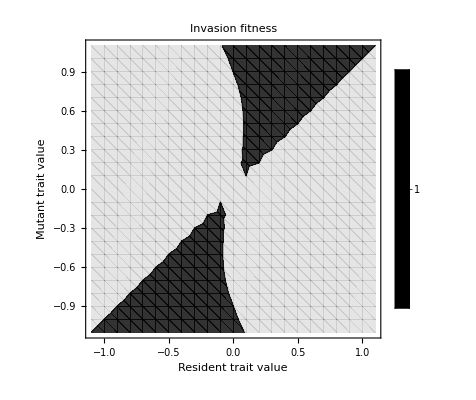

```mathematica
PairwiseInvasibilityPlot[lambda[y,x],dmg,init,{a->400,b->100,h->1,s->1,d->0.2,m->0.1,α->1},{-1.1,1.1,0.1},{Contours->{1}}]//Quiet
```

## Evolutionary singular strategies

### Selection gradient

Assuming rare mutations with small effects, the direction of evolution by selection is given by the selection gradient, which is the derivative of the invasion fitness function evaluated at the resident trait value. We derived a simplified expression for the selection gradient in the article:

```mathematica
v.MatrixForm[{{1-m,m}, {m,1-m}}.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}].u/(v.u)
G=v.{{1-m,m}, {m,1-m}}.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.u/(v.u);
```

(v.((1-m) dW_1 | m dW_2
m dW_1 | (1-m) dW_2).u)/(v.u)

where u and v are the right and left dominant eigenvectors of the transition matrix, respectively. They are given by

```mathematica
right=(Λ//Eigenvectors//Last) m Subscript[r, 1];
left=(Λ//Transpose//Eigenvectors//Last) m Subscript[r, 2];
```

which can be re-written in terms of λ:

```mathematica
λ-(1-m)Subscript[r, 2]==left[[1]]==right[[1]] //Simplify
left[[1]]=λ-(1-m)Subscript[r, 2]
right[[1]]=λ-(1-m)Subscript[r, 2]
```

True

-(1-m) r_2+1/2 (r_1-m r_1+r_2-m r_2+√((-r_1+m r_1-r_2+m r_2)^2-4 (r_1 r_2-2 m r_1 r_2)))

-(1-m) r_2+1/2 (r_1-m r_1+r_2-m r_2+√((-r_1+m r_1-r_2+m r_2)^2-4 (r_1 r_2-2 m r_1 r_2)))

And the selection gradient simplifies to

```mathematica
G=G/.u->right/.v->left/.λ->1//Simplify
gradient[x_]:=G/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.Subscript[dW, 1]->Subscript[dW, 1][x]/.Subscript[dW, 2]->Subscript[dW, 2][x]
```

(m^2 dW_2 r_1+dW_1 (1-m-(2-4 m+m^2) r_2+(1-3 m+2 m^2) r_2^2))/(1+(-2+2 m+m^2 r_1) r_2+(-1+m)^2 r_2^2)

where

```mathematica
Subscript[dW, 1][x_]:=D[Subscript[W, 1][y,x],y]/.y->x;
Subscript[dW, 2][x_]:=D[Subscript[W, 2][y,x],y]/.y->x;
```

We numerically check that this expression is equivalent to directly differentiating the invasion fitness function under some parameter values:

```mathematica
example = {a->400,b->100,h->1,s->1,d->0.2,m->0.1,α->1,x->0.34};
gradient[x]/.example/.FindRoot[dmg/.example,init]
D[lambda[y,x],y]/.y->x/.example/.FindRoot[dmg/.example,init]
```

-0.113684

-0.113684

Evolutionary singular strategies are trait values at which the selection gradient is zero. One can visualize how the selection gradient changes with the resident trait value,

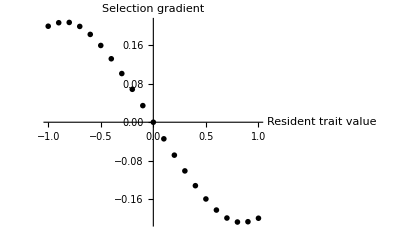

```mathematica
PlotSelectionGradient[gradient[x],dmg,init,{a->400,b->100,h->1,s->1,d->0.2,m->0.01,α->0}, {-1,1,0.1},{}]
```

### Convergence-stability

The slope of the selection gradient curve at a singular strategy determines if the strategy is convergence-stable, i.e. if it is evolutionarily attainable. The singular strategy is attainable from nearby trait values if the slope of the selection gradient is negative at the singular strategy, otherwise, that strategy is an evolutionary repellor. Here, we did not derive an explicit expression for the slope of the selection gradient at the singular strategy because we need explicit expressions for the change in equilibrium population densities as the resident strategy changes, and we could not derive those expressions because we could not solve other than numerically the system of third-order rational equations that gives the equilibrium population densities. Instead, we assessed convergence stability by measuring the difference in selection gradient slightly before and slightly after the singular strategy along the trait axis.

### Evolutionary stability

A singular strategy may not be invasion-proof, i.e. evolutionarily stable, even if selection leads to it from nearby resident trait values. The evolutionary stability of a singular strategy is determined by the sign of the curvature of the fitness function with respect to mutant trait values, evaluated at the singular strategy. If the curvature is negative, the singular strategy is a local fitness maximum and cannot be invaded by nearby mutants. If the curvature is positive, the singular strategy is a local minimum and can be invaded by any nearby mutant, thus favoring polymorphism and branching. We derived a simplified expression for the curvature of the fitness function at the singular strategy,

```mathematica
(dv.MatrixForm[M].MatrixForm[{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}].u + v.MatrixForm[M].MatrixForm[{{Subscript[ddW, 1]-α Subscript[W, 1],0},{0,Subscript[ddW, 2]-α Subscript[W, 2]}}].u + v.MatrixForm[M].MatrixForm[{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}].du)/(v.u)
F=(dv.M.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.u + v.M.{{Subscript[ddW, 1]-α Subscript[W, 1],0},{0,Subscript[ddW, 2]-α Subscript[W, 2]}}.u + v.M.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.du)/(v.u);
```

1/(v.u)(dv.(1-m | m
m | 1-m).(dW_1 | 0
0 | dW_2).u+v.(1-m | m
m | 1-m).(dW_1 | 0
0 | dW_2).du+v.(1-m | m
m | 1-m).(ddW_1-α W_1 | 0
0 | ddW_2-α W_2).u)

where the derivatives dv and du of the left and right eigenvectors are respectively given by the expressions:

```mathematica
dleft={(m-1)Subscript[dW, 2],m Subscript[dW, 2]};
dright={(m-1)Subscript[dW, 2],m Subscript[dW, 1]};
```

The fitness curvature at the singular strategy therefore simplifies to

```mathematica
F=F/.u->right/.v->left/.du->dright/.dv->dleft/.λ->1//Simplify
curvature[x_]:=F/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.Subscript[W, 1]->Subscript[W, 1][x,x]/.Subscript[W, 2]->Subscript[W, 2][x,x]/.Subscript[dW, 1]->Subscript[dW, 1][x]/.Subscript[dW, 2]->Subscript[dW, 2][x]/.Subscript[ddW, 1]->Subscript[ddW, 1][x]/.Subscript[ddW, 2]->Subscript[ddW, 2][x]
```

(m^2 ddW_2 r_1+2 (-1+2 m) dW_1 dW_2 (1+(-1+m) r_2)+ddW_1 (1-m-(2-4 m+m^2) r_2+(1-3 m+2 m^2) r_2^2)-α W_1+m α W_1+2 α r_2 W_1-4 m α r_2 W_1+m^2 α r_2 W_1-α r_2^2 W_1+3 m α r_2^2 W_1-2 m^2 α r_2^2 W_1-m^2 α r_1 W_2)/(1+(-2+2 m+m^2 r_1) r_2+(-1+m)^2 r_2^2)

where

```mathematica
Subscript[ddW, 1][x_]:=D[D[Subscript[W, 1][y,x],y],y]/.y->x
Subscript[ddW, 2][x_]:=D[D[Subscript[W, 2][y,x],y],y]/.y->x
```

We numerically checked that this expression gave the same result as directly differentiating the invasion fitness function, when evaluated at a singular strategy where the selection gradient is zero.

```mathematica
example = {a->400,b->100,h->1,s->1,d->0.2,m->0.1,α->1,x->0};
curvature[x]/.example/.FindRoot[dmg/.example,init]
D[D[lambda[y,x],y],y]/.y->x/.example/.FindRoot[dmg/.example,init]
gradient[x]==0/.example
```

0.2

0.2

True

We used the expressions for the selection gradient and the fitness curvature to numerically find singular strategies and evaluate their convergence-stability and invasion-proofness under various parameter sets.

```mathematica
EvaluateSingularStrategies[gradient[x],curvature[x],dmg,init,{a->400,b->100,h->1,s->1,d->0.2,m->0.1,α->1},{-1,1,0.1} ]
```

{{5.55112×10^-17,-0.0689463,0.2,3728.17,3728.17}}

Run the following script to explore singular strategies throughout parameter space and generate the data needed to produce Figure ... This may take several hours with a good resolution.

```mathematica
(* StringJoin[NotebookDirectory[], "ParamSpaceExploration1.m"]//Get; *)
```

## Within-patch dynamics with no dispersal

We applied the same procedure to the dynamics within each patch separately, assuming no dispersal. This allows disentangling across-patch branching due to within-patch disruptive selection or divergent stabilizing selection between the patches, when there is no dispersal. In this special case the within-patch geometric growth rate r_j(y,x) is the transition factor for the recursion equation of the population dynamics, and is also the invasion fitness.

```mathematica
Subscript[r, 1][y,x]
```

1-d+1/2 (1+ⅇ^(-(-x+y)^2 α)) ((a ⅇ^(-s (-1+y)^2) h)/(b+ⅇ^(-s (-1+x)^2) N_1)+(a ⅇ^(-s (1+y)^2))/(b+ⅇ^(-s (1+x)^2) N_1))

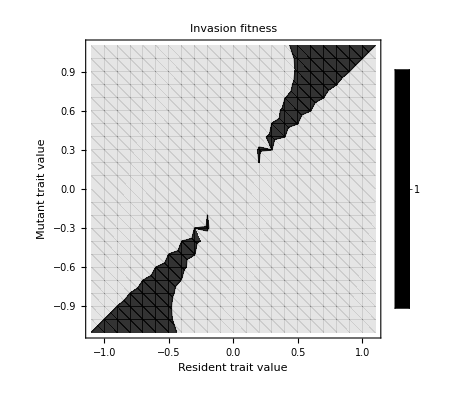

```mathematica
PairwiseInvasibilityPlot[Subscript[r, 1][y,x],Subscript[N, 1]==Subscript[r, 1][x,x] Subscript[N, 1],{Subscript[N, 1],1000},{a->400,b->100,h->1,s->1.5,d->0.2,α->0},{-1.1,1.1,0.1},{Contours->{1}}]//Quiet
```

We showed that the derivative of the within-patch growth rate is equal to the derivative of the reproductive success function when evaluated at the resident strategy.

```mathematica
D[Subscript[r, 1][y,x],y]==D[Subscript[W, 1][y,x],y]/.y->x
```

True

We therefore used the latter as a measure of the selection gradient.

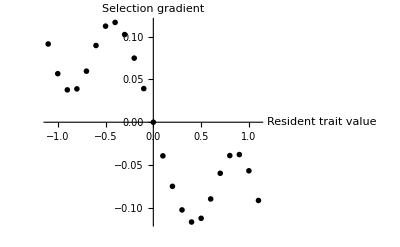

```mathematica
PlotSelectionGradient[Subscript[dW, 1][x],Subscript[N, 1]==Subscript[r, 1][x,x] Subscript[N, 1],{Subscript[N, 1],1000},{a->400,b->100,h->1,s->1.5,d->0.2,α->0},{-1.1,1.1,0.1},{}]
```

We showed that the curvature of the fitness function at the singular strategy can be simplified to

```mathematica
Subscript[ddW, 1][x]-α Subscript[W, 1][x,x];
```

which we can check by comparing to directly differentiating the invasion fitness and evaluating at a singular strategy.

```mathematica
example={a->400,b->100,h->1,s->1.5,d->0.2,α->0,x->0};
Subscript[ddW, 1][x]-α Subscript[W, 1][x,x]/.example/.FindRoot[Subscript[N, 1]==Subscript[r, 1][x,x]/.example,{Subscript[N, 1],1000}]
D[D[Subscript[r, 1][y,x],y],y]/.y->x/.example/.FindRoot[Subscript[N, 1]==Subscript[r, 1][x,x]/.example,{Subscript[N, 1],1000}]
```

10.6491

10.6491

We searched for singular strategies across various combinations of parameters, within the two patches separately, using the same procedures as for the two-patch model.

```mathematica
EvaluateSingularStrategies[Subscript[dW, 1][x],Subscript[ddW, 1][x]-α Subscript[W, 1][x,x],Subscript[N, 1]==Subscript[r, 1][x,x] Subscript[N, 1],{Subscript[N, 1],1000},{a->400,b->100,h->1,s->1.5,d->0.2,α->1},{-1.1,1.1,0.1} ]
```

{{0.,-0.078488,1.,3551.83}}

```mathematica
EvaluateSingularStrategies[Subscript[dW, 2][x],Subscript[ddW, 2][x]-α Subscript[W, 2][x,x],Subscript[N, 2]==Subscript[r, 2][x,x] Subscript[N, 2],{Subscript[N, 2],1000},{a->400,b->100,h->1,s->1.5,d->0.2,α->1},{-1.1,1.1,0.1} ]
```

{{0.,-0.078488,1.,3551.83}}

Run the following script for a thorough exploration of singular strategies within both patches across parameter space. This may take a few hours. The script was used to produce the data used in making Figure ...

```mathematica
(* StringJoin[NotebookDirectory[], "ParamSpaceExploration2.m"]//Get; *)
```

## Sensitivity to parameters

In addition, we ran the following scripts to produce pairwise invasibility plots in specific regions of parameter space, to illustrate the effects of certain parameters  on the stability of singular strategies (Fig. ... and ...). This may take a few minutes. The plots are shown below.

```mathematica
(* StringJoin[NotebookDirectory[], "PairwiseInvasibilityPlots1.m"]//Get; *)
(* StringJoin[NotebookDirectory[], "PairwiseInvasibilityPlots2.m"]//Get; *)
```

### Ecological divergent selection

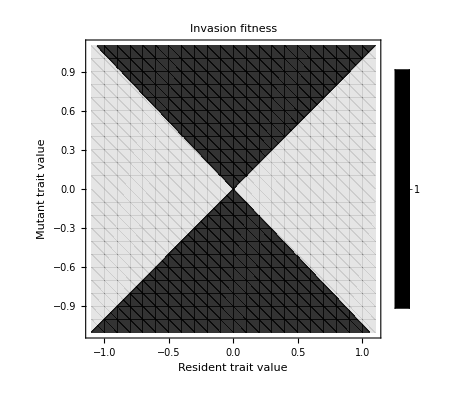
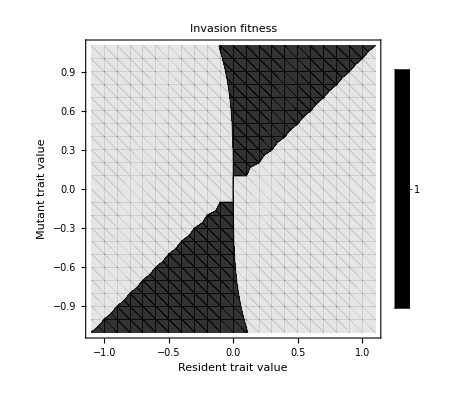
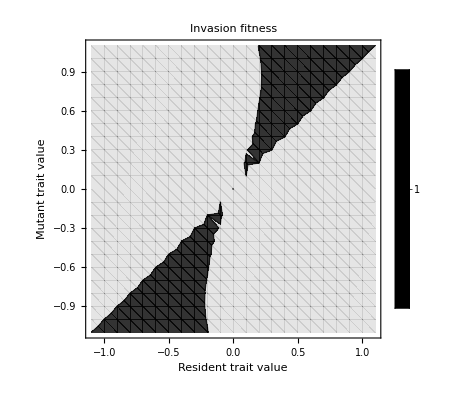
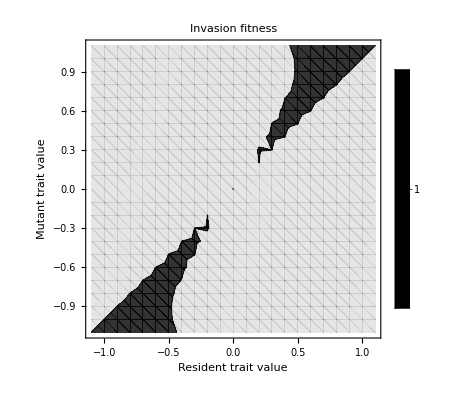
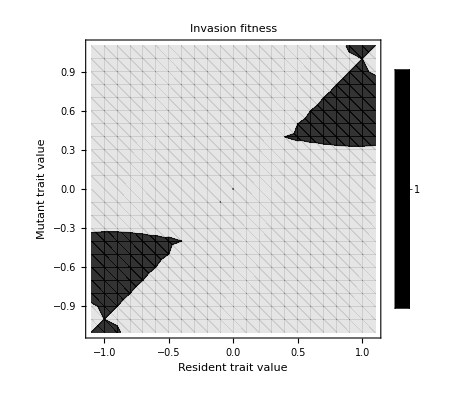
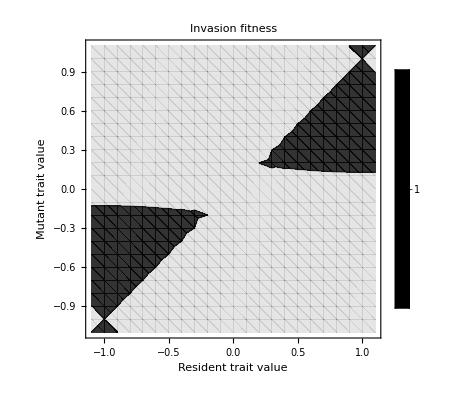

```mathematica
Map[PairwiseInvasibilityPlot[lambda[y,x],dmg,init,{a->400,b->100,h->1,s->#,m->0.01,d->0.2,α->0},{-1.1,1.1,0.1},{Contours->{1}}]&,{0.01,0.5,1,1.5,2,2.5}]//Quiet
```

### Sexual selection

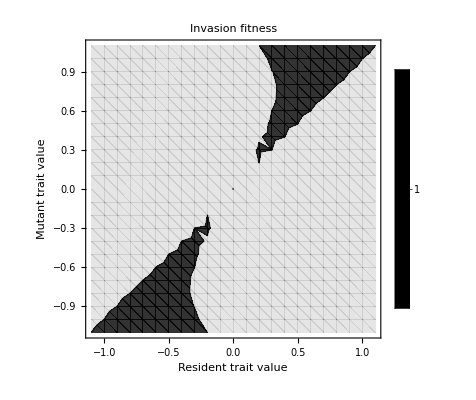
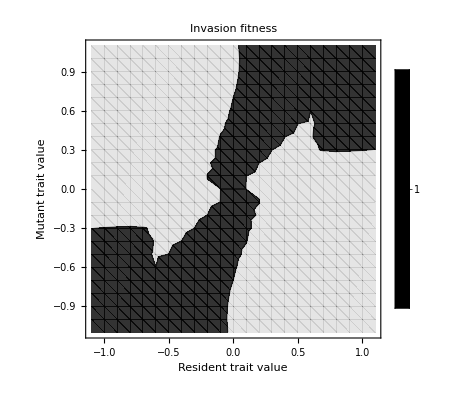
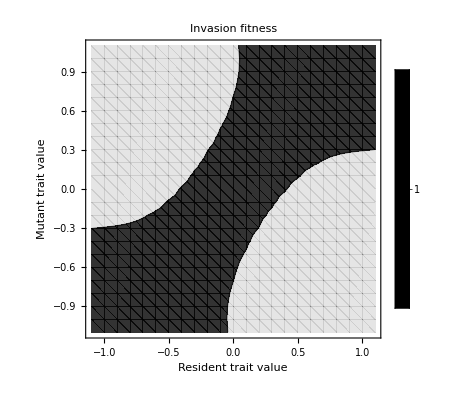
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[PairwiseInvasibilityPlot[lambda[y,x],dmg,init,{a->400,b->100,h->1,s->1.5,m->0.01,d->0.2,α->#},{-1.1,1.1,0.1},{Contours->{1}}]&,{0,1,10,100}]//Quiet
```